78.9 yr

```mathematica
"在世界地图中的图形"Entity["Country","UnitedStates"]Manipulate[Graphics[({EdgeForm[Brown],If[#1==="UnitedStates",Orange,LightBrown],Tooltip[CountryData[#1,{"SchematicPolygon","Robinson"}],{CountryData[#1,"Name"],CountryData[#1,prop]}]}&)/@CanonicalName[CountryData[]],ImageSize->500],{{prop,EntityProperty["Country","LifeExpectancy"],"国家属性"},Dynamic[CountryData["Properties"],SynchronousUpdating->False],ControlType->PopupMenu},SynchronousUpdating->False]
```

```mathematica
CountryData["UnitedStates", "LifeExpectancy"]
```

80.43 yr

```mathematica
data = DeleteCases[
					Table[
						{i, CountryData[i,"LifeExpectancy"]},
						{i,CountryData[All]}
						],
					{_,_,Missing}
	];
```

```mathematica
Short[data]
```

$Aborted

```mathematica
Short[SortBy[data, Last]]
```

{{Aland Islands,Missing[NotAvailable]},{Caribbean Netherlands,Missing[NotAvailable]},{Bouvet Island,Missing[NotAvailable]},{British Indian Ocean Territory,Missing[NotAvailable]},«241»,{Japan,84.65 yr},{Macau,84.81 yr},{Singapore,86.19 yr},{Monaco,89.4 yr}}

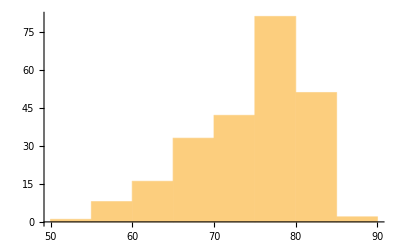

```mathematica
Histogram[data[[All, 2]]]
```

```mathematica
dataAfrica = DeleteCases[
						Table[
							{i, CountryData[i, "LifeExpectancy"]},
							{i, CountryData["Africa"]}
							],
						{_,_Missing}
];
Mean[dataAfrica[[All, 2]]]
```

66.4587 yr

```mathematica
dataAsia = DeleteCases[
					Table[
						{i, CountryData[i, "LifeExpectancy"]},
						{i, CountryData["Asia"]}
						],
					{_,_Missing}
];
```

```mathematica
Mean[dataAsia[[All, 2]]]
```

74.8257 yr

```mathematica
dataEurope = DeleteCases[
					Table[
						{i, CountryData[i, "LifeExpectancy"]},
						{i, CountryData["Europe"]}
						],
					{_,_Missing}
];
```

```mathematica
Mean[dataEurope]
```

{1/49 (Albania+Andorra+Austria+Belarus+Belgium+Bosnia and Herzegovina+Bulgaria+Croatia+Cyprus+Czech Republic+Denmark+Estonia+Faroe Islands+Finland+France+Germany+Gibraltar+Greece+Guernsey+Hungary+Iceland+Ireland+Isle of Man+Italy+Jersey+Kosovo+Latvia+Liechtenstein+Lithuania+Luxembourg+North Macedonia+Malta+Moldova+Monaco+Montenegro+Netherlands+Norway+Poland+Portugal+Romania+San Marino+Serbia+Slovakia+Slovenia+Spain+Sweden+Switzerland+Ukraine+United Kingdom),79.971 yr}

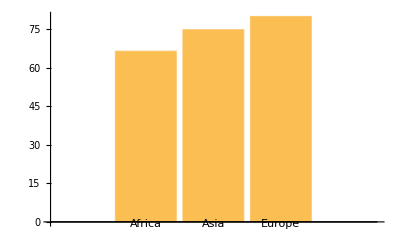

```mathematica
BarChart[
	{
		Mean[dataAfrica[[All, 2]]],
		Mean[dataAsia[[All, 2]]],
		Mean[dataEurope[[All, 2]]]	
      },
	ChartLabels->{"Africa", "Asia", "Europe"}
]
```

```mathematica
dataSouthAmerica = DeleteCases[
					Table[
						{i, CountryData[i, "LifeExpectancy"]},
						{i, CountryData["SouthAmerica"]}
						],
					{_,_,Missing}
];
```

```mathematica
Take[dataSouthAmerica, 3]
```

{{Argentina,78.07 yr},{Bolivia,70.7 yr},{Brazil,74.98 yr}}

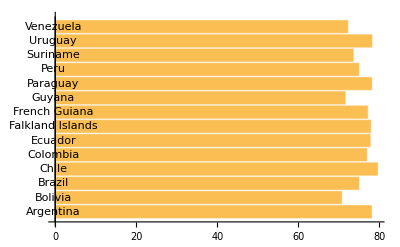

```mathematica
BarChart[
		dataSouthAmerica[[All, 2]],
		ChartLabels->dataSouthAmerica[[All, 1]],
		BarOrigin->Left
]
```

```mathematica
data = Table[
	Tooltip
		[
			{
				CountryData[i, "LifeExpectancy"],
				CountryData[i, "GDP"]
		      },
			CountryData[i,"Name"]
		],{i, CountryData[]}
];
```

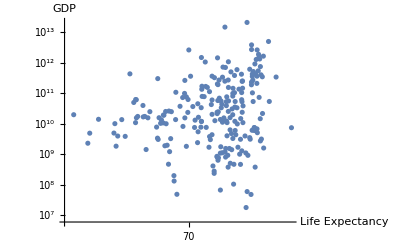

```mathematica
ListLogLogPlot[data, AxesLabel->{"Life Expectancy", "GDP"}]
```

```mathematica
data = Table[
	Tooltip
		[
			{
				CountryData[i, "LifeExpectancy"],
				CountryData[i, "InfantMortalityFraction"]
		      },
			CountryData[i,"Name"]
		],{i, CountryData[]}
];
```

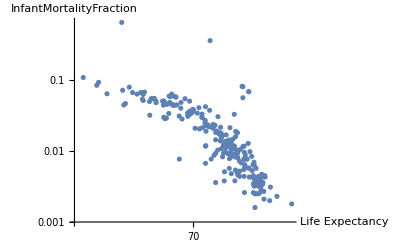

```mathematica
ListLogLogPlot[data, AxesLabel->{"Life Expectancy", "InfantMortalityFraction"}]
```

```mathematica
Manipulate[
            plotFn[
			Table[
					Tooltip[
						{
						CountryData[i, "LifeExpectancy"],
						CountryData[i,prop]
					      },
						  CountryData[i,"Name"]
					],
					{i,CountryData[All]}
				],
			AxesLabel->{"Life Expectancy", prop}
			],
			{prop,
				{
					"InfantMortalityFraction", 
					"GDP",
					 "LiteracyFraction"}
				},
			{
				{plotFn,ListLogLogPlot}, 
				{ListPlot, ListLogPlot, ListLogLogPlot}
		    },
	SaveDefinitions->True
]
```